# Projekt Temat: Model systemu produkcyjnego ze stanowiskami równoległymi i awariami. autorzy: Wojciech Waniek, Agata Musiał, Katarzyna Seifried, Karolina Bryłka

# System produkcyjny bez napraw.

Przedstawmy nasz system produkcyjny jako graf zorientowany, gdzie każdy wierzchołek odpowiada danemu komponentowi oraz wszystkie komponenty na początku działają.

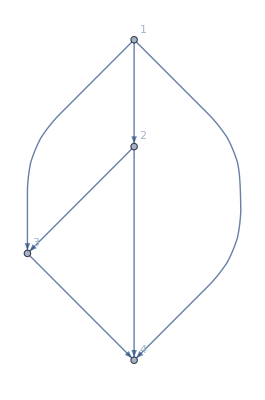

```mathematica
systemGraph=Graph[{1->2,1->3,1->4,2->3,2->4,3->4},VertexLabels->"Name"]
```

Zdefiniujmy teraz ścieżkę minimalną jako ścieżkę między początkiem, a końcem podanego systemu taką, że wszystkie komponenty tej ścieżki muszą działać, żeby system działał. Jeżeli jakikolwiek komponent ścieżki nie działa, to system też nie działa. 
Nasz system produkcyjny zawiera następujące ścieżki minimalne:

```mathematica
rowMinimalPaths=FindPath[systemGraph,1,4,Infinity,All]
```

{{1,4},{1,3,4},{1,2,4},{1,2,3,4}}

Niech x_i będzię zmienną informującą o tym, czy dany komponent działa, to znaczy x_i=1, jeżeli i-ty komponent działa i x_i=0 w przeciwynym przypadku. 
Teraz zdefiniujemy wektor stanu naszego systemu jako x=(x_1,…,x_n) oraz funkcję strukturalną Φ(x) wektora stanu x.
Funkcja strukturalna Φ(x)=1 dla danego wektora stanu x, jeżeli system działa i Φ(x)=0 w przypadku, gdy system nie działa.

Znajdziemy teraz funkcję strukturalną Φ naszego systemu. 

Niech funkcja strukturalna Φ będzie postaci:
Φ(x)=1-∏_(i∈A_j) (1-∏_(i∈A_j) x_i),
gdzie A_j to to minimalna ścieżka.

```mathematica
computeStructureFunction[systemGraph_,systemSource_,systemSink_]:=Module[{rowMinimalPaths,minimalPaths,stateVector,replaceVertexNumbersWithComponentState,pathStates,structureFunction},

replaceVertexNumbersWithComponentState[path_,stateVector_]:= stateVector[[#]]&/@path; (* Podstawiamy pod numer wierzchołka i zmienną Subscript[x, i]. *)

stateVector=Table[x[i],{i,VertexCount[systemGraph]}]; (* Tworzymy wektor stanu systemu x=(Subscript[x, 1],…,Subscript[x, n]). *)
rowMinimalPaths=FindPath[systemGraph,systemSource,systemSink,Infinity,All]; (* Znajdujemy wszystkie ścieżki pomiędzy wierzchołkiem początkowym i wierzchołkiem końcowym. *)
minimalPaths=replaceVertexNumbersWithComponentState[#,stateVector]&/@rowMinimalPaths; (* Tworzymy zbiór wszystkich takich ścieżek. *)
pathStates=Apply[Times,minimalPaths,{1}]; (* Tworzymy iloczyn ∏_(i∈Subscript[A, j]) Subscript[x, i]. *)
structureFunction=1-Apply[Times,1-pathStates]; (* Tworzymy iloczyn 1-∏_(i∈Subscript[A, j]) (1-∏_(i∈Subscript[A, j]) Subscript[x, i]). *)
structureFunction
]
structureFunction=computeStructureFunction[systemGraph,1,4]
```

1-(1-x[1] x[4]) (1-x[1] x[2] x[4]) (1-x[1] x[3] x[4]) (1-x[1] x[2] x[3] x[4])

Otrzymaliśmy funkcję strukturalną grafu w naszym przykładzie.

Zdefiniujmy teraz funkcję niezawodności jako r(p)=P(Φ(x)=1), gdzie p=(p_1,…,p_n) to wektor prawdopodobieństw działania poszczególnych komponentów.

```mathematica
computeReliabilityFunction[structureFunction_]:=Module[{reliabilityFunction},
Clear[p];
reliabilityFunction=Expand[structureFunction]/.a_^p_:>a ;(* Rozwijamy funkcję strukturalną na sumę wielomianów.
x[i] ma rozkład Bernoulliego, więc to x[i]^2=x[i]. Podstawiamy x^n[i]->x[i],n∈ℕ .*)
reliabilityFunction/.x->p 
]

reliabilityFunction=computeReliabilityFunction[structureFunction]
```

p[1] p[4]

Otrzymaliśmy rozwiązanie, że aby system działał, tylko działanie komponentów 1 i 4 ma znaczenie.

Teraz zdefiniujmy funkcję opisującą czas działania komponentu F_i jako F_i(t)=P{ "czas działania komponentu i" >t}=P{ "komponent i działa w chwili t" }. Zakładamy, że po wystąpieniu awarii komponent nie ulega naprawie.
Funkcja opisująca czas działania całego systemu dana jest wzorem F̄(t)=P{ “czas dzialania systemu”>t }=P{ “system działa w chwili t” }=r(F_1,…,F_n)=1-F(t), gdzie F(t) jest dystrybuantą, a n liczbą komponentów

Zakładamy teraz, że czas działania każdego komponentu ma rozkład wykładniczy z intensywnością λ.
W naszym przykładzie przyjmijmy λ=0.2.

(1-(Piecewise[{{1-ⅇ^(-0.2 t), t≥0}, {0, True}}]))^2

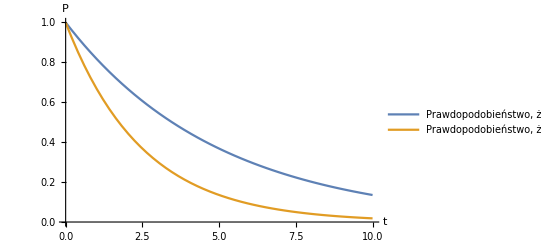

```mathematica
ClearAll;
intensity=0.2;
exponentialSurvivalFunction=1-CDF[ExponentialDistribution[intensity],t]; (* Obliczamy funkcję Subscript[F, i] każdego komponentu. *)
componentsSurvivalFunctions=Table[exponentialSurvivalFunction,{VertexCount[systemGraph]}]; (* Tworzymy wektor (Subscript[F, 1],…,Subscript[F, n]). *)

ComputeSurvivalFunction[componentsSurvivalFunctions_,reliabilityFunction_]:=Module[{systemSurvivalFunction,systemLifeTimePDF},
For[i=1,i<=Length[componentsSurvivalFunctions],i++,p[i]=componentsSurvivalFunctions[[i]]]; (* Tworzymy pętlę obliczającą funkcję r(Subscript[F, 1],…,Subscript[F, n]). *)
systemSurvivalFunction=Evaluate[reliabilityFunction];
systemSurvivalFunction
] ;

systemSurvivalFunction=ComputeSurvivalFunction[componentsSurvivalFunctions,reliabilityFunction]
Plot[{exponentialSurvivalFunction,systemSurvivalFunction},{t,0,10},AxesLabel->{t,P},AxesStyle->Arrowheads[0.03],PlotLegends->{"Prawdopodobieństwo, że komponent działa w chwili t.","Prawdopodobieństwo, że system działa w chwili t."}]
```

Otrzymaliśmy wykres prawdopodobieństwa działania jednego komponentu oraz systemu w czasie t.

Weźmy inny przykład.

Tym razem zakładamy, że czas działania każdego komponentu ma rozkład jednostajny z parametrami λ i μ.
Przyjmijmy λ=5 i μ=10.

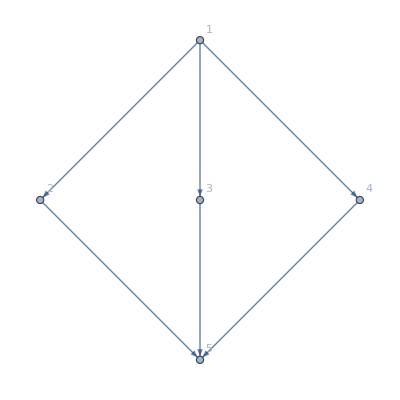

1-(1-x[1] x[2] x[5]) (1-x[1] x[3] x[5]) (1-x[1] x[4] x[5])

p[1] p[2] p[5]+p[1] p[3] p[5]-p[1] p[2] p[3] p[5]+p[1] p[4] p[5]-p[1] p[2] p[4] p[5]-p[1] p[3] p[4] p[5]+p[1] p[2] p[3] p[4] p[5]

3 (1-(Piecewise[{{1/5 (-5+t), 5≤t≤10}, {1, t>10}, {0, True}}]))^3-3 (1-(Piecewise[{{1/5 (-5+t), 5≤t≤10}, {1, t>10}, {0, True}}]))^4+(1-(Piecewise[{{1/5 (-5+t), 5≤t≤10}, {1, t>10}, {0, True}}]))^5

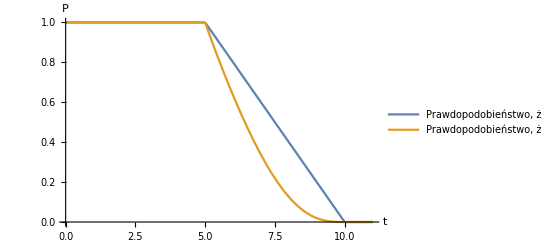

```mathematica
ClearAll;
systemGraph=Graph[{1->2,1->3,1->4,2->5,3->5,4->5},VertexLabels->"Name"]
structureFunction=computeStructureFunction[systemGraph,1,5] 
reliabilityFunction=computeReliabilityFunction[structureFunction] 

uniformSurvivalFunction=1-CDF[UniformDistribution[{5,10}],t];
componentsSurvivalFunctions=Table[uniformSurvivalFunction,{VertexCount[systemGraph]}]; 

systemSurvivalFunction=ComputeSurvivalFunction[componentsSurvivalFunctions,reliabilityFunction]
Plot[{uniformSurvivalFunction,systemSurvivalFunction},{t,0,11},AxesLabel->{t,P},AxesStyle->Arrowheads[0.03],PlotLegends->{"Prawdopodobieństwo, że komponent działa w chwili t.","Prawdopodobieństwo, że system działa w chwili t."}]
```

A teraz przyjmijmy, że czas działania komponentów jest zdefiniowany przy pomocy różnych rozkładów prawdopodobieństwa.

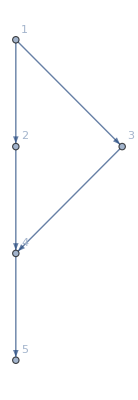

1-(1-x[1] x[2] x[4] x[5]) (1-x[1] x[3] x[4] x[5])

p[1] p[2] p[4] p[5]+p[1] p[3] p[4] p[5]-p[1] p[2] p[3] p[4] p[5]

(1-(Piecewise[{{1-ⅇ^(-0.3 t), t≥0}, {0, True}}]))^2 (1-(Piecewise[{{GammaRegularized[1+Floor[t],3.5], t≥0}, {0, True}}])) (1-(Piecewise[{{1/7 (-3+t), 3≤t≤10}, {1, t>10}, {0, True}}]))+(1-(Piecewise[{{1-ⅇ^(-0.3 t), t≥0}, {0, True}}]))^2 (1-(Piecewise[{{1/7 (-3+t), 3≤t≤10}, {1, t>10}, {0, True}}]))^2-(1-(Piecewise[{{1-ⅇ^(-0.3 t), t≥0}, {0, True}}]))^2 (1-(Piecewise[{{GammaRegularized[1+Floor[t],3.5], t≥0}, {0, True}}])) (1-(Piecewise[{{1/7 (-3+t), 3≤t≤10}, {1, t>10}, {0, True}}]))^2

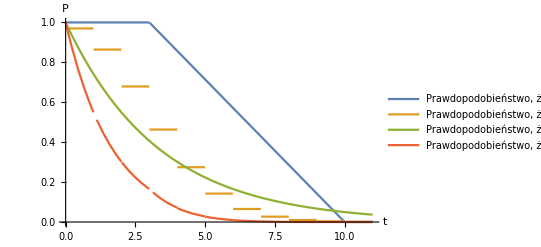

```mathematica
ClearAll;
systemGraph=Graph[{1->2,1->3,3->4,2->4,4->5},VertexLabels->"Name"]
structureFunction=computeStructureFunction[systemGraph,1,5] 
reliabilityFunction=computeReliabilityFunction[structureFunction] 

f1=1-CDF[UniformDistribution[{3,10}],t];
f2=1-CDF[PoissonDistribution[3.5],t];
f3=1-CDF[ExponentialDistribution[0.3],t];
componentsSurvivalFunctions={f1,f1,f2,f3,f3};

systemSurvivalFunction=ComputeSurvivalFunction[componentsSurvivalFunctions,reliabilityFunction]
Plot[{f1,f2,f3,systemSurvivalFunction},{t,0,11},AxesLabel->{t,P},AxesStyle->Arrowheads[0.03],PlotLegends->{"Prawdopodobieństwo, że komponenty 1 i 2 działają w chwili t.","Prawdopodobieństwo, że komponent 3 działa w chwili t.","Prawdopodobieństwo, że komponenty 4 i 5 działają w chwili t.","Prawdopodobieństwo, że system działa w chwili t."}]
```

# System produkcyjny z naprawami.

Zakładamy, że początkowo wszystkie komponenty działają i że czas działania ka komponentów ma rozkład wykładniczy z intensywnością λ, a czas naprawy wszystkich komponentu  ma rozkład wykładniczy z intensywnością μ. 

Teraz zdefiniujmy funkcję dyspozycyjności jako A(t)=P{  "system działa w chwili t"  }=r{A_1(t),…,A_n(t)}, gdzie A_i(t)=P{ " komponent i działa w chwili t "}, a r(A) jest funkcją niezawodności.
Wyznaczymy wartość A_i(t) za pomocą wzoru A_i(t)=μ_i/(μ_i+λ_i)+λ_i/(μ_i+λ_i)ⅇ^(-(μ_i+λ_i)t).

Wykorzystamy pierwszy przykład z poprzedniego przypadku. 
Przyjmijmy λ=0.2, μ=0.1.

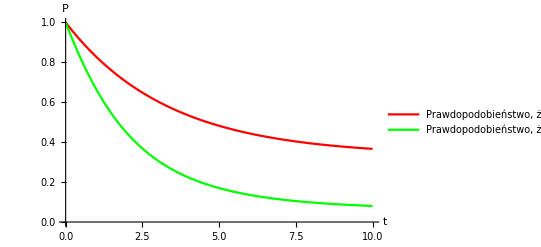

```mathematica
CreateAvailabilityFunction[intensityFunctioning_,intensityRepairing_]:=intensityRepairing/(intensityFunctioning+intensityRepairing)+intensityFunctioning/(intensityFunctioning+intensityRepairing)*ⅇ^(-(intensityFunctioning+intensityRepairing)*t);

intensityFunctioning=0.2;
intensityRepairing=0.1;

exponentialAvailabilityFunction=CreateAvailabilityFunction[intensityFunctioning,intensityRepairing]; (* Obliczamy funkcję dyspozycyjności Subscript[A, i] dla każdego komponentu i. *)
componentsAvailabilityFunctions=Table[exponentialAvailabilityFunction,{VertexCount[systemGraph]}]; (* Tworzymy wektor (Subscript[A, 1],...,Subscript[A, n]). *)

reliabilityFunction=computeReliabilityFunction[structureFunction]; (* Definiujemy funkcję niezawodności. *)

ComputeAvailabilityFunction[componentsAvailabilityFunctions_,reliabilityFunction_]:=Module[{systemAvailabilityFunction},
Clear[p];
For[i=1,i<=Length[componentsAvailabilityFunctions],i++,p[i]=componentsAvailabilityFunctions[[i]]]; (* Tworzymy pętlę obliczającą funkcję r(Subscript[A, 1],…,Subscript[A, n]). *)
systemAvailabilityFunction=Evaluate[reliabilityFunction];
systemAvailabilityFunction
] ;

Plot[{exponentialAvailabilityFunction,systemAvailabilityFunction},{t,0,10},PlotStyle->{Red,Green},AxesOrigin->{0,0},AxesLabel->{t,P},AxesStyle->Arrowheads[0.03],PlotLegends->{"Prawdopodobieństwo, że komponent działa w chwili t.","Prawdopodobieństwo, że system działa w chwili t."}]
```

Przeprowadźmy podobne rozumowanie na innym przykładzie.

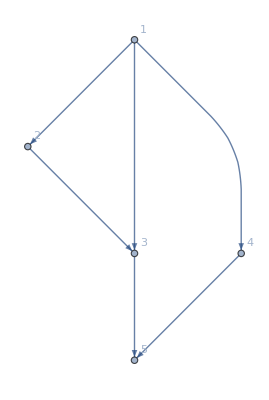

1-(1-x[1] x[3] x[5]) (1-x[1] x[2] x[3] x[5]) (1-x[1] x[4] x[5])

p[1] p[3] p[5]+p[1] p[4] p[5]-p[1] p[3] p[4] p[5]

2 (0.25+0.75 ⅇ^(-0.4 t))^3-(0.25+0.75 ⅇ^(-0.4 t))^4

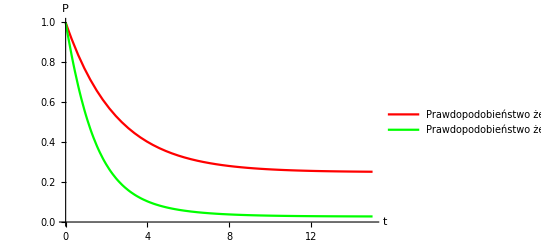

```mathematica
ClearAll;
systemGraph=Graph[{1->2,1->3,1->4,2->3,3->5,4->5},VertexLabels->"Name"]

structureFunction=computeStructureFunction[systemGraph,1,5]
reliabilityFunction=computeReliabilityFunction[structureFunction]

intensityFunctioning=0.3;
intensityRepairing=0.1;

reliabilityFunction=computeReliabilityFunction[structureFunction];

exponentialAvailabilityFunction=CreateAvailabilityFunction[intensityFunctioning,intensityRepairing];

componentsAvailabilityFunctions=Table[exponentialAvailabilityFunction,{VertexCount[systemGraph]}];

systemAvailabilityFunction=ComputeAvailabilityFunction[componentsAvailabilityFunctions,reliabilityFunction]
Plot[{exponentialAvailabilityFunction,systemAvailabilityFunction},{t,0,15},PlotStyle->{Red,Green},AxesOrigin->{0,0},AxesLabel->{t,P},AxesStyle->Arrowheads[0.03],PlotLegends->{"Prawdopodobieństwo że komponent działa w chwili t","Prawdopodobieństwo że system działa w chwili t"}]
```

bibliografia: “Intorduction to Probability Models 10th Edition” Sheldon M. Ross